# Mathematical Modeling of Epidemic Data

-Graphics-

Enter the equations:

```mathematica
equationS=s'[t]==-b s[t] i[t]
```

s'[t]==-b i[t] s[t]

```mathematica
equationI=i'[t]==b s[t]i[t]-k i[t]
```

i'[t]==-k i[t]+b i[t] s[t]

```mathematica
i'[t]==-k i[t]+b i[t] s[t]
```

i'[t]==-k i[t]+b i[t] s[t]

```mathematica
equationR=r'[t]==k i[t]
```

r'[t]==k i[t]

The parameters b (the probability of infection) and k (the amount of time to recover) determine the rate of change between the compartments.

Enter initial values:

```mathematica
b=.5
k=1/14
```

0.5

1/14

Use NDSolve to get a solution:

```mathematica
solution=NDSolve[{equationS,equationI,equationR,s[0]==0.9999,i[0]==0.0001,r[0]==0.0000},{s,r,i},{t,100}]
```

{{s→InterpolatingFunction[…],r→InterpolatingFunction[…],i→InterpolatingFunction[…]}}

Generate an individual graph for each variable:

```mathematica
solutionS=First[s/.solution]
solutionI=First[i/.solution];
solutionR=First[r/.solution];
```

InterpolatingFunction[…]

Plot the solution:

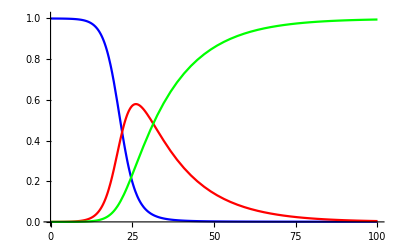

```mathematica
Plot[{solutionS[t],solutionI[t],solutionR[t]},{t,0,100},PlotRange->{0,1.01},PlotStyle->{Blue,Red,Green}]
```

Vary the parameters:

```mathematica
solution=Manipulate[Show[Plot[#[t],{t,0,100},PlotRange->All,AxesOrigin->{0,0}]&/@Values@Flatten@Block[{b=x,
k=y},NDSolve[{equationS,equationI,equationR,s[0]==0.9999,i[0]==0.0001,r[0]==0.0000},{s,r,i},{t,100}]]],{x,0,1},{y,0,1}]
```

Analyze a textbook influenza dataset:

```mathematica
influenzaData=;
```

Get a feel for what the data contains:

```mathematica
Keys@%
```

{NumberBoys,NumberConfinedToBed,NumberConvelescent,NumberNotInClass}

```mathematica
influenzaData
```

<|NumberBoys→763,NumberConfinedToBed→{{Sun 22 Jan 1978,0},{Mon 23 Jan 1978,6},{Tue 24 Jan 1978,26},{Wed 25 Jan 1978,74},{Thu 26 Jan 1978,223},{Fri 27 Jan 1978,294},{Sat 28 Jan 1978,258},{Sun 29 Jan 1978,237},{Mon 30 Jan 1978,191},{Tue 31 Jan 1978,124},{Wed 1 Feb 1978,68},{Thu 2 Feb 1978,27},{Fri 3 Feb 1978,12},{Sat 4 Feb 1978,4}},NumberConvelescent→{{Wed 25 Jan 1978,0},{Thu 26 Jan 1978,8},{Fri 27 Jan 1978,16},{Sat 28 Jan 1978,99},{Sun 29 Jan 1978,161},{Mon 30 Jan 1978,173},{Tue 31 Jan 1978,163},{Wed 1 Feb 1978,150},{Thu 2 Feb 1978,89},{Fri 3 Feb 1978,45},{Sat 4 Feb 1978,23}},NumberNotInClass→512|>

```mathematica
firstDate=First@First@influenzaData["NumberConfinedToBed"]
lastDate=First@Last@influenzaData["NumberConfinedToBed"]
```

Sun 22 Jan 1978

Sat 4 Feb 1978

```mathematica
fitData={QuantityMagnitude[DateDifference[firstDate,#1]],#2}&@@@influenzaData["NumberConfinedToBed"]//Echo[#,"",Multicolumn]&;
```

{0,0} | {4,223} | {8,191} | {12,12}
{1,6} | {5,294} | {9,124} | {13,4}
{2,26} | {6,258} | {10,68} | 
{3,74} | {7,237} | {11,27} |

```mathematica
populationSize=influenzaData["NumberBoys"]
```

763

Visualize the data:

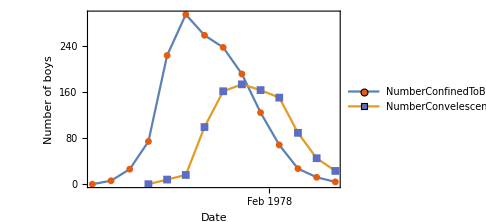

```mathematica
DateListPlot[KeyTake[influenzaData,{"NumberConfinedToBed","NumberConvelescent"}],FrameLabel->{"Date","Number of boys"},ImageSize->Medium,PlotMarkers->{-Graphics-,-Graphics-}]
```

Set up the data fitting:

```mathematica
ClearAll[b,k]
```

```mathematica
forceOfInfectionSIR={λ[t_]:>i[t]};
{susceptibleSIR,infectedSIR,recoveredSIR}={s,i,r}/.ParametricNDSolve[Join[{equationS,equationI,equationR}/.forceOfInfectionSIR,{s[0]==𝒩-i0,i[0]==i0,r[0]==0}],{s,i,r},{t,0,100},{𝒩,i0,b,k}];
```

Create a dynamic module to manually try to fit the data:

```mathematica
DynamicModule[{localData,localPop,localSusceptible,localInfected,localRecovered,b,k,tMax=50},localPop=populationSize;
localData=fitData;
{localSusceptible,localInfected,localRecovered}={susceptibleSIR,infectedSIR,recoveredSIR};
Manipulate[b=10.^logb;
k=10.^logk;
Show[Plot[{localSusceptible[localPop,1,b,k][t],localInfected[localPop,1,b,k][t],localRecovered[localPop,1,b,k][t]},{t,0,tmax},PlotRange->{All,{0,500}},PlotLegends->{s,i,r},PlotStyle->{ColorData["Crayola"]["Blue"],ColorData["Crayola"]["Red"],ColorData["Crayola"]["Green"]}],ListPlot[localData,PlotStyle->ColorData["Crayola"]["Red"]]],{{logb,Log10@0.003,Dynamic@StringForm["b = `` (infection)",TraditionalForm[10.^logb]]},Log10@0.0001,Log10@1.0},{{logk,Log10@0.43,Dynamic@StringForm["k = `` (recovery)",TraditionalForm[10.^logk]]},Log10@(1/5),Log10@(1/(*1*)0.1)},Delimiter,{{tmax,15,"t_max"},5,tMax},{{ymax,800,"y_max"},50,800}]]
```

Use NonlinearModelFit to get a proper fit:

```mathematica
fit=NonlinearModelFit[fitData,infectedSIR[populationSize,1,b,k][t],{{b,0.0025},{k,0.48}},t]
```

FittedModel[InterpolatingFunction[…][t]]

Plot the fit and visualize the fit versus the data:

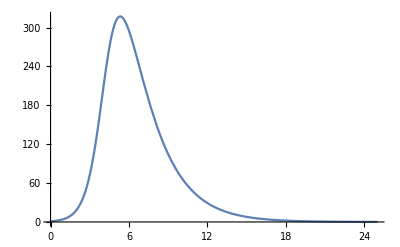

```mathematica
fittedPlot=Plot[fit[t],{t,0,25},PlotRange->All]
```

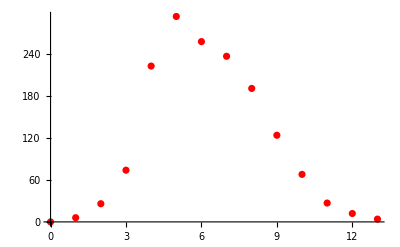

```mathematica
fitDataPlot=ListPlot[fitData,PlotStyle->Red]
```

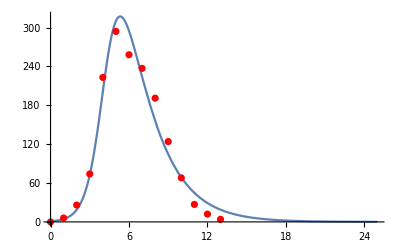

```mathematica
Show[fittedPlot,fitDataPlot]
```